## setup

### overhead

```mathematica
(* clear all variable names and assignments *)
Clear["Global`*"];ClearAll["Global`*"];Remove["Global`*"];ClearSystemCache[];
```

```mathematica
(* directory of Mathematica files *)
dirMathematica=Environment["HOME"]<>"/Mathematica_files/";

(* ln-fhs "/Users/dantopa/Dropbox/_mm" "/Users/dantopa/Mathematica_files" *)

(* packages shared by all notebooks *)
dirnb=dirMathematica<>"nb/";
dirPack=dirnb<>"packages/";

(* seed file *)
nbSeed="seed 19_12.nb";
```

### tag

```mathematica
home="ert/rcs/fourier/"; 
Get["utility modules.m",Path->dirPack];
stamp1;
```

CreateDirectory::filex: /home/dantopa/Mathematica_files/io/ already exists.

CreateDirectory::filex: /home/dantopa/Dropbox/_mm/io/ert/ already exists.

CreateDirectory::filex: /home/dantopa/Dropbox/_mm/io/ert/rcs/ already exists.

General::stop: Further output of CreateDirectory::filex will be suppressed during this calculation.

maximum memory: 0.0798735 GB

seed file: /home/dantopa/Mathematica_files/nb/seed 19_12.nb

user: dantopa, CPU: dtopa-latitude-5491,  MM v. 12.0.0 for Linux x86

date: Mar 10, 2020, time: 10:45:16

nb: /home/dantopa/Mathematica_files/nb/ert/rcs/fourier/rapido-03.nb

### modules, functions, settings, ...

#### admin

```mathematica
printmem
```

maximum memory: 0.0798735 GB

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```

#### settings

```mathematica
exportFlag=True;
```

```mathematica
o={0,0};
```

```mathematica
guc=Circle[o,1];
```

```mathematica
fticks={{Automatic,Automatic},{{{1,-π},{91,-π/2},{181,0},{271,π/2},{361,π}},Automatic}};
nticks={{Automatic,Automatic},{π/2 ints,Automatic}};
```

```mathematica
𝕔=299792458;
```

#### functions

```mathematica
Clear[sty];
sty[s_String]:=Style[s,FontFamily->"TimesNewRoman"]
```

#### substitutions

#### modules

## import

```mathematica
meanRCS=Import[dirData<>"rcs-values.dat"];
```

## data

### grab slice

```mathematica
ν=9;
index=ν-2;
λ=Round[𝕔/(ν 1000000)]
%//N
```

33

33.

```mathematica
rcs=meanRCS[[index]];
m=Length[rcs];
```

```mathematica
Mean[rcs]
mx=Max[rcs]
mn=Min[rcs]
{top,bot}={1.1mx,0.9mn};
```

18.8395

39.4069

3.35132

```mathematica
σ=RotateLeft[rcs,180];
```

```mathematica
Θ=Table[
k π/180
,{k,-180,180}];
m=Length[Θ]
```

361

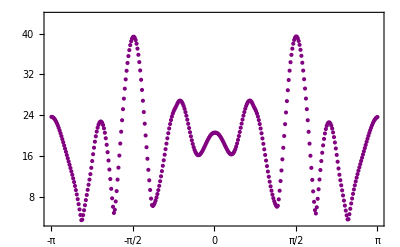

```mathematica
gσ=ListPlot[σ,
PlotRange->{bot,top},
Frame->True,
FrameTicks->fticks,
PlotStyle->Purple]
```

```mathematica
tag=sty["ν = "<>ToString[ν]<>" MHz, λ = "<>ToString[λ]<>" m"];
```

```mathematica
z={Θ,σ}ᵀ;
g000=ListPlot[z,PlotStyle->{Purple,Opacity[0.5],PointSize[0.005]}];
```

## 1 compose linear system

### maximum expansion order

```mathematica
ω=25;
```

```mathematica
avector=Table[Cos[j θ],{j,0,ω}];
bvector=Join[avector,Table[Sin[j θ],{j,ω}]];
```

```mathematica
masterA=Table[
Simplify[avector/.θ->Θ[[k]]]
,{k,m}];
```

### sweep expansion order d

```mathematica
Λ=1.1;
```

```mathematica
te={};
myAmplitudes={};
myErrors={};
G={};
minTE=∞;
Do[
Print[lf,"d = ",d];
(* define Hilbert space basis functions *)
vector=Take[avector,d+1];
(* grab slice of master matrix *)
A=Take[masterAᵀ,d+1]ᵀ;
(* compute Fourier-Bessel coefficients *)
c=LeastSquares[A,σ];
AppendTo[myAmplitudes,c];
(* approximation function *)
Clear[f];
f[θ_]=c.vector;
(* approximation vector *)
F=f[θ]/.θ->Θ;
(* residual error *)
r=σ-F;
(* total error *)
r2=r.r;
If[r2<minTE,minTE=r2;where=d];
AppendTo[te,r2];
(* uncertainty propagation *)
ϵ=√(r2/(m-(d+1))Diagonal[Inverse[A†.A//N]]);
AppendTo[myErrors,ϵ];
(* signal to noise *)
γ=Last[c]/Last[ϵ];
AppendTo[G,{d,γ}];
(* graphics *)
(* function *)
g001=Plot[f[θ],{θ,-π,π},
Frame->True,
PlotRange->{bot,top},
FrameTicks->nticks,
PlotStyle->{Opacity[0.25],Blue}];
(* compare *)
ga=Show[{g001,g000},
PlotLabel->sty["MoM RCS vs Fourier Cosine Expansion"],
FrameLabel->{sty["Nose angle"],sty["Mean total RCS"]},
Epilog->{Text[sty["d = "<>ToString[d]],{0.95π,1.05mx},{1,0},Background->White],Text[sty["ν = "<>ToString[ν]<>" MHz"],{-0.95π,1.05mx},{-1,0},Background->White],Text[sty["λ = "<>ToString[λ]<>" m"],{-0.95π,1.02mx},{-1,0},Background->White]},
ImageSize->6 72];
(* residual error *)
gb=ListPlot[r,
Frame->True,
FrameTicks->fticks,
FrameLabel->{sty["Nose angle"],sty["Residual error"]},
PlotRange->Λ{-1,1},
PlotStyle->{Red,PointSize[0.005]},
PlotLabel->sty["Fourier Approximation Error"],
Epilog->{Text[sty["d = "<>ToString[d]],{350,0.80Λ},{1,0},Background->White],Text[sty["ν = "<>ToString[ν]<>" MHz"],{10,0.80Λ},{-1,0},Background->White],Text[sty["λ = "<>ToString[λ]<>" m"],{10,0.67Λ},{-1,0},Background->White]},
ImageSize->6 72];
(* group plots *)
gout=GraphicsRow[{ga,gb},
ImageSize->14 72];
(* output *)
tresExport["rcs-cos-"<>pad[ν]<>"-"<>pad[d],gout]
,{d,ω}]
```

d = 1

d = 2

d = 3

d = 4

d = 5

d = 6

d = 7

d = 8

d = 9

$Aborted

```mathematica
minTE
where
```

9.80907

25

```mathematica
ϵ
```

{0.00900764,0.0127232,0.0127232,0.0127232,0.0127232,0.0127232,0.0127232,0.0127232,0.0127232,0.0127232,0.0127232,0.0127232,0.0127232,0.0127232,0.0127232,0.0127232,0.0127232,0.0127232,0.0127232,0.0127232,0.0127232,0.0127232,0.0127232,0.0127232,0.0127232,0.0127232}

```mathematica
G
```

{{1,4.63628},{2,-11.0389},{3,-3.00912},{4,52.0402},{5,-16.5626},{6,52.6563},{7,-20.8511},{8,12.6408},{9,4.72812},{10,-8.58649},{11,3.76958},{12,-2.84577},{13,-0.334307},{14,0.621649},{15,-1.19489},{16,0.730836},{17,-0.690679},{18,0.21202},{19,-0.28558},{20,0.0224113},{21,-0.190314},{22,0.0371186},{23,-0.198289},{24,0.0694876},{25,-0.186954}}

```mathematica
.......
```

## summary

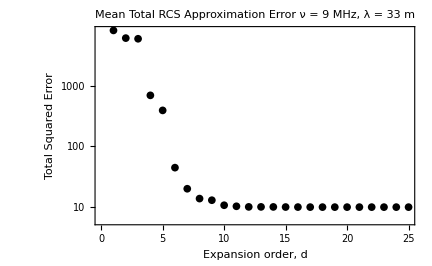

```mathematica
pTotalError=ListLogPlot[te,
Frame->True,
PlotStyle->Black,
ImageSize->6 72,
PlotLabel->Style["Mean Total RCS Approximation Error"<>lf<>"ν = "<>ToString[ν]<>" MHz, λ = "<>ToString[λ]<>" m",FontFamily->"TimesNewRoman"],
FrameLabel->{sty["Expansion order, d"],sty["Total Squared Error"]}
]
```

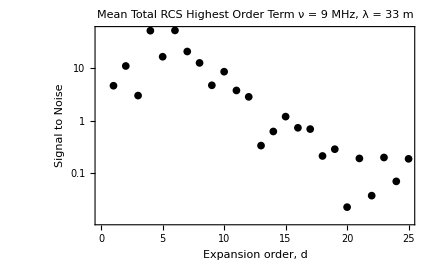

```mathematica
pSignalNoise=ListLogPlot[Abs[G],
Frame->True,
PlotStyle->Black,
ImageSize->6 72,
PlotLabel->Style["Mean Total RCS Highest Order Term"<>lf<>"ν = "<>ToString[ν]<>" MHz, λ = "<>ToString[λ]<>" m",FontFamily->"TimesNewRoman"],
FrameLabel->{sty["Expansion order, d"],sty["Signal to Noise"]}
]
```

```mathematica
tresExport["rcs-cos-total-error-"<>pad[ν]<>"-"<>pad[ω],pTotalError];
tresExport["rcs-cos-signal-to-noise-"<>pad[ν]<>"-"<>pad[ω],pSignalNoise];
```

## end

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```